Remove::rmptc: Symbol ℛos5500head is Protected and cannot be removed.

Remove::rmptc: Symbol ℛrh1288 is Protected and cannot be removed.

Remove::rmptc: Symbol ℛrh2288 is Protected and cannot be removed.

General::stop: Further output of Remove::rmptc will be suppressed during this calculation.

{ℛrh1288,ℛrh2288,ℛos5500head}

Piecewise[{{1, t<0}, {ⅇ^(-5.174×10^-6 t) (1-(1-ⅇ^(-3.425×10^-6 t))^2) (1-(1-ⅇ^(-2.×10^-6 t))^2) (1-(1-ⅇ^(-3.62×10^-7 t))^2)^2 (ⅇ^(-1.746×10^-6 t)+ⅇ^(-5.82×10^-7 t) (-ⅇ^(-1.746×10^-6 t)+ⅇ^(-1.164×10^-6 t)+ⅇ^(-5.82×10^-7 t) (-ⅇ^(-1.164×10^-6 t)+ⅇ^(-5.82×10^-7 t)+ⅇ^(-5.82×10^-7 t) (1-ⅇ^(-5.82×10^-7 t))))), True}}]

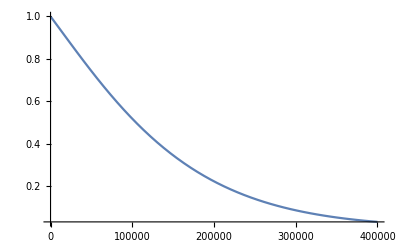

132564.

{0.999992,0.99997,0.999819,0.999457}

15.1329

```mathematica
removeAll:=Remove[Evaluate[$Context<>"*"]];
Protect[ℛrh1288,ℛrh2288,ℛos5500head];
removeAll
Unprotect[ℛrh1288,ℛrh2288,ℛos5500head]

(* Считаем для сервера RH1288 *)
Remove[Evaluate[$Context<>"*"]];

Dataset[{
<|"1 - A"->"MB (MotherBoard)","2 - B"->"RAID","3 - C"->"CPU","4 - D"->"RAM","5 - E"->"FAN","6 - F"->"HDD",
"7 - G"->"PS (Power Supply)","8 - H"->"NET","9 - I"->"FC (Fiber Channel)"|>}];

(* задаем распределения для каждого компонента отдельно *)
dists=Flatten [{{{Subscript[x, 1],ExponentialDistribution[4035×10^-9]}, {Subscript[x, 2],ExponentialDistribution[559×10^-9]}},Array[{Subscript[c, #],ExponentialDistribution[40×10^-9]}&,2], Array[{Subscript[d, #],ExponentialDistribution[50×10^-9]}&,10], Array[{Subscript[e, #],ExponentialDistribution[582×10^-9]}&,4],Array[{Subscript[f, #],ExponentialDistribution[3425×10^-9]}&,2],Array[{Subscript[g, #],ExponentialDistribution[2000×10^-9]}&,2],Array[{Subscript[h, #],ExponentialDistribution[362×10^-9]}&,2],Array[{Subscript[i, #],ExponentialDistribution[362×10^-9]}&,2]} ,1] //N;
(* bexpr=And @@Array[Subscript[x, #]&,9] *)
Subscript[x, 3]=And @@Array[Subscript[c, #]&,2]; (* CPU *)
Subscript[x, 4]=And @@Array[Subscript[d, #]&,10]; (* RAM *)
Subscript[x, 5]=BooleanCountingFunction[{3,4},4]@@Array[Subscript[e, #]&,4] //BooleanConvert ;(* FAN *)
Subscript[x, 6]=Or @@Array[Subscript[f, #]&,2]; (* HDD *)
Subscript[x, 7]=Or @@Array[Subscript[g, #]&,2]; (* PS *)
Subscript[x, 8]=Or @@Array[Subscript[h, #]&,2]; (* NET *)
Subscript[x, 9]=Or @@Array[Subscript[i, #]&,2]; (* FC *)
bexpr=And @@Array[Subscript[x, #]&,9];
(* Проверим логическую связь *)
unateQ[bexpr];
ℛrh1288=ReliabilityDistribution[bexpr,dists];
SurvivalFunction[ℛrh1288,t]
Plot[SurvivalFunction[ℛrh1288,t]//Evaluate,{t,0,400000},PlotRange->All]
(* mttf=NExpectation[t,t\[Distributed]ℛrh1288] (* идентично mttf=Mean[ℛrh1288] *) *)
mttf = Mean[ℛrh1288] //N
avail = mttf/(mttf+{1,4,24,72})
mttf/(24*365)
```

Piecewise[{{1, t<0}, {ⅇ^(-5.174×10^-6 t) (1-(1-ⅇ^(-2.306×10^-6 t))^2) (1-(1-ⅇ^(-2.×10^-6 t))^2) (1-(1-ⅇ^(-3.62×10^-7 t))^2)^2 (ⅇ^(-1.746×10^-6 t)+ⅇ^(-5.82×10^-7 t) (-ⅇ^(-1.746×10^-6 t)+ⅇ^(-1.164×10^-6 t)+ⅇ^(-5.82×10^-7 t) (-ⅇ^(-1.164×10^-6 t)+ⅇ^(-5.82×10^-7 t)+ⅇ^(-5.82×10^-7 t) (1-ⅇ^(-5.82×10^-7 t))))), True}}]

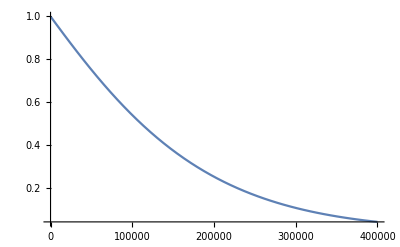

142970.

{0.999993,0.999972,0.999832,0.999497}

16.3207

```mathematica
(* Считаем для сервера RH2288 *)
Remove[Evaluate[$Context<>"*"]];

Dataset[{
<|"1 - A"->"MB (MotherBoard)","2 - B"->"RAID","3 - C"->"CPU","4 - D"->"RAM","5 - E"->"FAN","6 - F"->"SSD",
"7 - G"->"PS (Power Supply)","8 - H"->"NET","9 - I"->"FC (Fiber Channel)"|>}];

(* задаем распределения для каждого компонента отдельно *)
dists=Flatten [{{{Subscript[x, 1],ExponentialDistribution[4035×10^-9]}, {Subscript[x, 2],ExponentialDistribution[559×10^-9]}},Array[{Subscript[c, #],ExponentialDistribution[40×10^-9]}&,2], Array[{Subscript[d, #],ExponentialDistribution[50×10^-9]}&,10], Array[{Subscript[e, #],ExponentialDistribution[582×10^-9]}&,4],Array[{Subscript[f, #],ExponentialDistribution[2306×10^-9]}&,2],Array[{Subscript[g, #],ExponentialDistribution[2000×10^-9]}&,2],Array[{Subscript[h, #],ExponentialDistribution[362×10^-9]}&,2],Array[{Subscript[i, #],ExponentialDistribution[362×10^-9]}&,2]} ,1] //N;
(* bexpr=And @@Array[Subscript[x, #]&,9] *)
Subscript[x, 3]=And @@Array[Subscript[c, #]&,2]; (* CPU *)
Subscript[x, 4]=And @@Array[Subscript[d, #]&,10]; (* RAM *)
Subscript[x, 5]=BooleanCountingFunction[{3,4},4]@@Array[Subscript[e, #]&,4] //BooleanConvert ;(* FAN *)
Subscript[x, 6]=Or @@Array[Subscript[f, #]&,2]; (* HDD *)
Subscript[x, 7]=Or @@Array[Subscript[g, #]&,2]; (* PS *)
Subscript[x, 8]=Or @@Array[Subscript[h, #]&,2]; (* NET *)
Subscript[x, 9]=Or @@Array[Subscript[i, #]&,2]; (* FC *)
bexpr=And @@Array[Subscript[x, #]&,9];
(* Проверим логическую связь *)
unateQ[bexpr];
ℛrh2288=ReliabilityDistribution[bexpr,dists];
SurvivalFunction[ℛrh2288,t]
Plot[SurvivalFunction[ℛrh2288,t]//Evaluate,{t,0,400000},PlotRange->All]
(* mttf=NExpectation[t,t\[Distributed]ℛrh2288] (* идентично mttf=Mean[ℛrh2288] *) *)
mttf = Mean[ℛrh2288] //N
avail = mttf/(mttf+{1,4,24,72}) 
mttf/(24*365)
```

Piecewise[{{1, t<0}, {(1-(1-ⅇ^(-4.035×10^-6 t))^2) (1-(1-ⅇ^(-2.×10^-6 t))^2) (1-(1-ⅇ^(-4.×10^-8 t))^2) (ⅇ^(-0.00001153 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-0.00001153 t)+ⅇ^(-9.224×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-9.224×10^-6 t)+ⅇ^(-6.918×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-6.918×10^-6 t)+ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t)+ⅇ^(-2.306×10^-6 t) (1-ⅇ^(-2.306×10^-6 t))))))+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-0.00001153 t)+ⅇ^(-9.224×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-9.224×10^-6 t)+ⅇ^(-6.918×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-6.918×10^-6 t)+ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t)+ⅇ^(-2.306×10^-6 t) (1-ⅇ^(-2.306×10^-6 t)))))+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-9.224×10^-6 t)+ⅇ^(-6.918×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-6.918×10^-6 t)+ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t)+ⅇ^(-2.306×10^-6 t) (1-ⅇ^(-2.306×10^-6 t))))+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-6.918×10^-6 t)+ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t)+ⅇ^(-2.306×10^-6 t) (1-ⅇ^(-2.306×10^-6 t)))+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t)+ⅇ^(-2.306×10^-6 t) (1-ⅇ^(-2.306×10^-6 t))+ⅇ^(-2.306×10^-6 t) (1-ⅇ^(-2.306×10^-6 t)-ⅇ^(-2.306×10^-6 t) (1-ⅇ^(-2.306×10^-6 t)))-ⅇ^(-2.306×10^-6 t) (-ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t)+ⅇ^(-2.306×10^-6 t) (1-ⅇ^(-2.306×10^-6 t))))-ⅇ^(-2.306×10^-6 t) (-ⅇ^(-6.918×10^-6 t)+ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t)+ⅇ^(-2.306×10^-6 t) (1-ⅇ^(-2.306×10^-6 t)))))-ⅇ^(-2.306×10^-6 t) (-ⅇ^(-9.224×10^-6 t)+ⅇ^(-6.918×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-6.918×10^-6 t)+ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t)+ⅇ^(-2.306×10^-6 t) (1-ⅇ^(-2.306×10^-6 t))))))-ⅇ^(-2.306×10^-6 t) (-ⅇ^(-0.00001153 t)+ⅇ^(-9.224×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-9.224×10^-6 t)+ⅇ^(-6.918×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-6.918×10^-6 t)+ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t) (-ⅇ^(-4.612×10^-6 t)+ⅇ^(-2.306×10^-6 t)+ⅇ^(-2.306×10^-6 t) (1-ⅇ^(-2.306×10^-6 t)))))))), True}}]

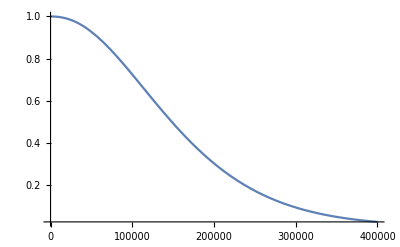

164998.

{0.999994,0.999976,0.999855,0.999564}

18.8354

```mathematica
(* Считаем для контроллера СХД *)
Remove[Evaluate[$Context<>"*"]];

Dataset[{
<|"1 - A"->"MB (MotherBoard)","2 - B"->"CPU","3 - C"->"PS (Power Supply)","4 - D"->"SSD 1.8","5 - E"->"HDD 4","6 - F"->"HDD 1.2"|>}];

(* задаем распределения для каждого компонента отдельно *)
dists=Flatten [{Array[{Subscript[a, #],ExponentialDistribution[4035×10^-9]}&,2],Array[{Subscript[b, #],ExponentialDistribution[40×10^-9]}&,2] ,Array[{Subscript[c, #],ExponentialDistribution[2000×10^-9]}&,2], Array[{Subscript[d, #],ExponentialDistribution[2306×10^-9]}&,5+2] } ,1] //N;
(* bexpr=And @@Array[Subscript[x, #]&,9] *)
Subscript[x, 1]=Or @@Array[Subscript[a, #]&,2]; (* MB *)
Subscript[x, 2]=Or @@Array[Subscript[b, #]&,2]; (* CPU *)
Subscript[x, 3]=Or @@Array[Subscript[c, #]&,2]; (* PS *)
Subscript[x, 4]=BooleanCountingFunction[{5,5+2},5+2]@@Array[Subscript[d, #]&,5+2] //BooleanConvert; (* HDD 1.8*)
bexpr=And @@Array[Subscript[x, #]&,4];
(* Проверим логическую связь *)
unateQ[bexpr];
ℛos5500head=ReliabilityDistribution[bexpr,dists];
SurvivalFunction[ℛos5500head,t]
Plot[SurvivalFunction[ℛos5500head,t]//Evaluate,{t,0,400000},PlotRange->All]
(* mttf=NExpectation[t,t\[Distributed]ℛos5500head] *)
mttf=Mean[ℛos5500head] //N
avail = mttf/(mttf+{1,4,24,72})
mttf/(24*365)//N
```

Piecewise[{{1, t<0}, {ⅇ^(-8357 t/40000000) (-53194089192720+811209860188980 ⅇ^(137 t/40000000)-5774714258972400 ⅇ^(137 t/20000000)+25455205957654200 ⅇ^(411 t/40000000)-77705365554944400 ⅇ^(137 t/10000000)+174004515010536210 ⅇ^(137 t/8000000)-295280389108788720 ⅇ^(411 t/20000000)+386676700023413800 ⅇ^(959 t/40000000)-393972486816308400 ⅇ^(137 t/5000000)+312315796172757300 ⅇ^(1233 t/40000000)-191063781188039760 ⅇ^(137 t/4000000)+88584116732636616 ⅇ^(1507 t/40000000)-30130651949876400 ⅇ^(411 t/10000000)+7098086276653575 ⅇ^(1781 t/40000000)-1035587055560400 ⅇ^(959 t/20000000)+70539987842520 ⅇ^(411 t/8000000)), True}}]

Piecewise[{{1, t<0}, {ⅇ^(-6439 t/40000000) (38910617655-477078007770 ⅇ^(137 t/40000000)+2682238577018 ⅇ^(137 t/20000000)-9143995148925 ⅇ^(411 t/40000000)+21052453947525 ⅇ^(137 t/10000000)-34485924561660 ⅇ^(137 t/8000000)+41214885451740 ⅇ^(411 t/20000000)-36210220789743 ⅇ^(959 t/40000000)+23211679993425 ⅇ^(137 t/5000000)-10587783856650 ⅇ^(1233 t/40000000)+3262182053130 ⅇ^(137 t/4000000)-609599676595 ⅇ^(1507 t/40000000)+52251400851 ⅇ^(411 t/10000000)), True}}]

87975.4

{0.999989,0.999955,0.999727,0.999182}

10.0429

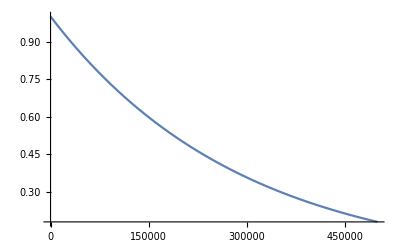

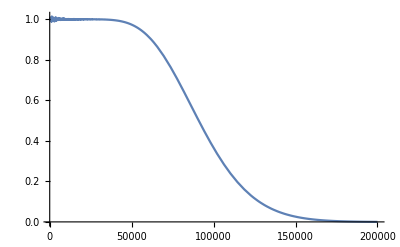

```mathematica
(* Считаем диски OS5500 для НЦ *)
(* Сочиняем ручками SurvivalFunction для резервирования с дробной кратностью *)
Remove[Evaluate[$Context<>"*"]];
DiskSurvival[P_,N_, K_]:= ∑_(i=0)^K (Binomial[N+K,i]*(1-P)^i*(P)^(N+K-i))
Subscript[p, 1]=SurvivalFunction[ExponentialDistribution[3425×10^-9],t]; (* 4 Tb *)
Subscript[p, 2]=SurvivalFunction[ExponentialDistribution[3425×10^-9],t];(* 1.2 Tb *)
subdisk1=DiskSurvival[Subscript[p, 1],46,15] //Simplify
subdisk2=DiskSurvival[Subscript[p, 2],35,12] //Simplify

Mean[pp] //N;
(* mttf=∫_0^∞ subdisk1 * subdisk2ⅆt //N *)
 mttf=∫_0^∞ subdisk1ⅆt //N 
avail = mttf/(mttf+{1,4,24,72})
mttf/(24*365)//N (* в годах *)
Plot[Subscript[p, 1],{t,0,500000},PlotRange->All]
Plot[subdisk2,{t,500,200000},PlotRange->All]
```

122533.

{0.999992,0.999967,0.999804,0.999413}

13.9878

-Graphics-

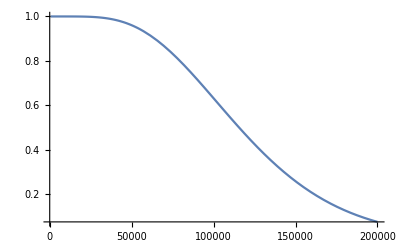

```mathematica
(* Считаем диски OS5500 для РНИЦ *)
(* Сочиняем ручками SurvivalFunction для резервирования с дробной кратностью *)
Remove[Evaluate[$Context<>"*"]];
DiskSurvival[P_,N_, K_]:= ∑_(i=0)^K (Binomial[N+K,i]*(1-P)^i*(P)^(N+K-i))
Subscript[p, 1]=SurvivalFunction[ExponentialDistribution[3425×10^-9],t]; (* 4 Tb *)
Subscript[p, 2]=SurvivalFunction[ExponentialDistribution[3425×10^-9],t];(* 1.2 Tb *)
subdisk1=DiskSurvival[Subscript[p, 1],23,8] //Simplify;
subdisk2=DiskSurvival[Subscript[p, 2],12,5] //Simplify;

Mean[pp] //N;
(* mttf=∫_0^∞ subdisk1 * subdisk2ⅆt //N *)
 mttf=∫_0^∞ subdisk2ⅆt //N 
avail = mttf/(mttf+{1,4,24,72})
mttf/(24*365)//N (* в годах *)
Plot[Subscript[p, 1],{t,0,500000},PlotRange->All]
Plot[subdisk2,{t,500,200000},PlotRange->All]
```

```mathematica
(* Расчет готовности узлов, подключенных по мажоритарной системе *)
(* Мажоритарные системы.Мажоритарную систему («схему голосования» или «m из n») можно рассматривать как вариант системы с параллельным соединением,отказ которой произойдет,если из n элементов,соединенных параллельно,работоспособными окажутся менее m элементов.Мажоритарные системы часто встречаются в технологических линиях,системах управления,гидро-и пневмосистемах,электрических схемах,а также при структурном резервировании. *)
```

```mathematica
availRH2288={0.999972,0.999832,0.999497}; (* 4, 24, 72 часа *)
availRH1288={0.999970,0.9998189,0.999457}; (* 4, 24, 72 часа *)
Print["НЦ, виртуализация 4+4"];
n=8;m=4;
p=availRH2288;
(* p=0.9999 *)
Ptotal=∑_(k=m)^n Binomial[n,k] p^k(1-p)^(n-k) 
1.-NumberForm[1-Ptotal,30]
Print["НЦ, app 2+1, virt mngmnt 2+1"];
n=3;m=2;
p=availRH1288;
(* p=0.9999 *)
Ptotal=∑_(k=m)^n Binomial[n,k] p^k(1-p)^(n-k) 
1.-NumberForm[1-Ptotal,30]

Print["РНИЦ, виртуализация 1+1"];
n=2;m=1;
p=availRH2288;
(* p=0.9999 *)
Ptotal=∑_(k=m)^n Binomial[n,k] p^k(1-p)^(n-k) 
1.-NumberForm[1-Ptotal,30]
Print["НЦ, app 4+1"];
n=5;m=4;
p=availRH1288;
(* p=0.9999 *)
Ptotal=∑_(k=m)^n Binomial[n,k] p^k(1-p)^(n-k) 
1.-NumberForm[1-Ptotal,30]




(* ================= END ================== *)
```

НЦ, виртуализация 4+4

{1.,1.,1.}

1.-{1.110223024625157×10^-16,-2.220446049250313×10^-16,1.887379141862766×10^-15}

НЦ, app 2+1, virt mngmnt 2+1

{1.,1.,0.999999}

1.-{2.6999460445154×10^-9,9.83797509013229×10^-8,8.84226794006793×10^-7}

РНИЦ, виртуализация 1+1

{1.,1.,1.}

1.-{7.839999760506089×10^-10,2.822400002600034×10^-8,2.530089999730478×10^-7}

НЦ, app 4+1

{1.,1.,0.999997}

1.-{8.99946006605035×10^-9,3.278533247108584×10^-7,2.945289243716509×10^-6}

```mathematica
NumberForm[0.9999990000000001,16]
```

0.999999

```mathematica
NumberForm[0.9999000000020001,16]
```

0.999900000002

```mathematica
(* Считаем для дисков СХД НЦ *)
(* ТАК НЕ РАБОТАЕТ, см правильное ниже *)
Protect[ℛrh1288,ℛrh2288,ℛos5500head];Remove[Evaluate[$Context<>"*"]];Unprotect[ℛrh1288,ℛrh2288,ℛos5500head]

Dataset[{
<|"1 - A"->"HDD 4","2 - B"->"HDD 1.2"|>}];
aTypeMin=46; aTypeZIP=15; aTypeMax=aTypeMin+ aTypeZIP;
bTypeMin=35; bTypeZIP=11; bTypeMax=bTypeMin+ bTypeZIP;

(* задаем распределения для каждого компонента отдельно *)
(* Subscript[a, 1]=ExponentialDistribution[3425×10^-9]; 
Subscript[a, 2]=ExponentialDistribution[3425×10^-9];
Subscript[p, 1]=PDF[BinomialDistribution[aTypeMax,Subscript[a, 1]],aTypeMin] (* HDD 4 *)
Subscript[p, 2]=PDF[BinomialDistribution[bTypeMax,Subscript[a, 2]],bTypeMin] (* HDD 1.2 *) *)

dists=Flatten [{Array[{Subscript[a, #],ExponentialDistribution[3425×10^-9]}&,aTypeMax],Array[{Subscript[b, #],ExponentialDistribution[3425×10^-9]}&,bTypeMax] } ,1];

Subscript[x, 1]=BooleanCountingFunction[{aTypeMin,aTypeMax},aTypeMax]@@Array[Subscript[a, #]&,aTypeMax] //BooleanConvert; (* HDD 4 *)
Subscript[x, 2]=BooleanCountingFunction[{bTypeMin,bTypeMax},bTypeMax]@@Array[Subscript[b, #]&,bTypeMax]//BooleanConvert; (* HDD 1.2 *) 

ℛos5500ncdisk=ReliabilityDistribution[Subscript[x, 1] && Subscript[x, 2],dists];
SurvivalFunction[ℛos5500ncdisk,t];
(* mttf=NExpectation[t,t\[Distributed]ℛos5500head] *)
mttf=Mean[ℛos5500ncdisk] //N
avail = mttf/(mttf+{1,4,24,72})
mttf/(24*365)//N
```

Remove::rmptc: Symbol ℛos5500head is Protected and cannot be removed.

Remove::rmptc: Symbol ℛrh1288 is Protected and cannot be removed.

Remove::rmptc: Symbol ℛrh2288 is Protected and cannot be removed.

General::stop: Further output of Remove::rmptc will be suppressed during this calculation.

{ℛrh1288,ℛrh2288,ℛos5500head}

```mathematica
Plot[SurvivalFunction[ℛos5500ncdisk,t]//Evaluate,{t,0,200000},PlotRange->All]
```

```mathematica
Subscript[p, 1]
```

```mathematica
(* см. http://mathematica.stackexchange.com/questions/63763/create-a-probabilitydistribution *)
PDF[BinomialDistribution[n,p],k]
```

```mathematica
(* Считаем для НЦ *)
```

```mathematica
Subscript[x, 1]=And @@Array[Subscript[a, #]&,2]; (* AR2240 *)
Subscript[x, 2]=And @@Array[Subscript[b, #]&,10]; (* CE6851 *)
Subscript[x, 3]=And @@Array[Subscript[c, #]&,2]; (* S5320 *)
Subscript[x, 4]=And @@Array[Subscript[d, #]&,10]; (* SNS2224 *)
Subscript[x, 5]=BooleanCountingFunction[{4,8},8]@@Array[Subscript[v, #]&,8] //BooleanConvert ;(* virt *)
Subscript[x, 6]=BooleanCountingFunction[{2,3},3]@@Array[Subscript[ap, #]&,3] //BooleanConvert ;(* app *)
Subscript[x, 7]=BooleanCountingFunction[{1,3},3]@@Array[Subscript[vm, #]&,3] //BooleanConvert ;(* virt-mng *)
Subscript[x, 8]=Or @@Array[Subscript[f, #]&,2]; (* OS5500-controller *)
Subscript[x, 9]=BooleanCountingFunction[{46,46+15},46+15]@@Array[Subscript[g, #]&,46+15] && BooleanCountingFunction[{35,35+11},35+11]@@Array[Subscript[h, #]&,35+11] (* OS5500-disk 4Tb + 1.2Tb*)
bexpr=And @@Array[Subscript[x, #]&,9]
```

```mathematica
(* всякие исследования *)
Subscript[z, 1]=SurvivalFunction[ExponentialDistribution[λ],t];
Binomial[50,15]
BooleanCountingFunction[{46,46+15},46+15]@@Array[Subscript[g, #]&,46+15] //BooleanConvert
```